```mathematica
n=2;q=n/2;P=Sqrt[((-q)^2)-(0.5^2)];L1=-q+P;L2=-q-P;X=0.2;X0=L2*X-1;Z=1/(2*P);A=X0-(L2*X);B=X0-(L1*X);a[t_]:=Z*(((A+(L2*X))*Exp[t*L1])-((B+(L1*X))*Exp[t*L2]));b[t_]:=Z*((A+L2*X)*Exp[t*L1]);c[t_]:=Z*(-(B+L1*X)*Exp[t*L2]);
j[t_]:=Z*((A-X0)*Exp[t*L1]-(B-X0)*Exp[t*L2]);k[t_]:=Z*((A-X0)*Exp[t*L1]);l[t_]:=Z*(-(B-X0)*Exp[t*L2]);x[t_]:=a[t]+j[t];(*x[t_]:=Z*(A*Exp[t*L1]-B*Exp[t*L2])*);y[t_]:=b[t]+k[t];(*y[t_]:=Z*(A*Exp[t*L1])*);z[t_]:=c[t]+l[t];(*z[t_]:=Z*(-B*Exp[t*L2])*);
Solve[x[t]==0,t];
(1/(L2-L1))*Log[A/B]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

0.171728

```mathematica
Solve[x[t]==0,t];
(1/(L2-L1))*Log[A/B]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

-1.89185

```mathematica
{{t->2.6982989551687857+1.813799364234218 ⅈ}}
```

{{t→2.6983+1.8138 ⅈ}}

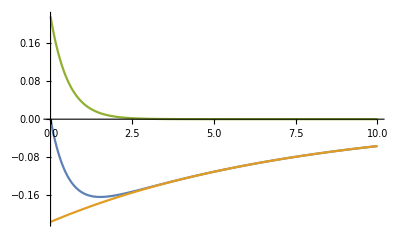

```mathematica
Plot[{a[t],b[t],c[t]}, {t,0,10}]
```

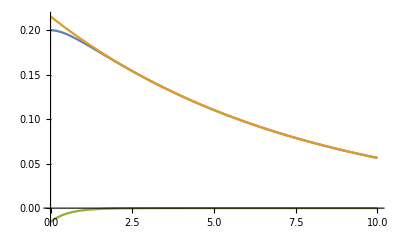

```mathematica
Plot[{j[t],k[t],l[t]}, {t,0,10}]
```

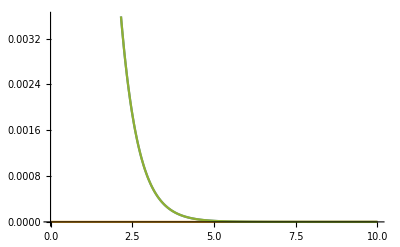

```mathematica
Plot[{x[t],y[t],z[t]}, {t,0,10}]
```

```mathematica
(*Plot[{a[t],b[t],c[t],j[t],k[t],l[t],x[t],y[t],z[t]},{t,0,1}]*)
```

```mathematica
Manipulate[{Exp[-t*n/2],Exp[P*t],Exp[-P*t],(Exp[P*t]-Exp[-P*t]),Exp[-t*n/2]*(Exp[P*t]-Exp[-P*t])},{t,0,10}]
```

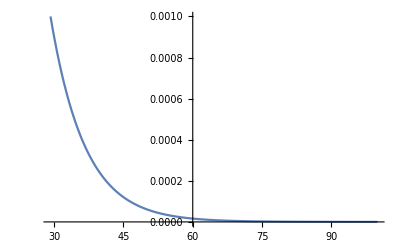

```mathematica
Plot[x[t],{t,0,100},PlotRange->{{60,65},{0.001,-0.001}}]
```

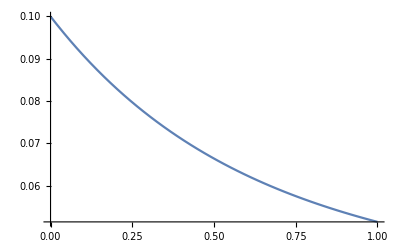

```mathematica
Plot[x[t],{t,0,1}]
```

```mathematica
Manipulate[x[t],{t,0,100}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→1.3352+1.8138 ⅈ}}

```mathematica
{{t->0.1339307122899659+1.813799364234218 ⅈ}}
```

{{t→0.133931+1.8138 ⅈ}}

```mathematica
0.1/e
```

```mathematica
0.1/e
```

0.1/e

```mathematica
e
```

e

```mathematica
E
```

ⅇ

```mathematica
0.1/E
```

```mathematica
1.036787944117144235
```

```mathematica
0.1/Sqrt[E]
```

0.0606531

```mathematica
0.1+(0.1/Sqrt[E])
```

0.160653

```mathematica
0.1/E
```

```mathematica
0.136787944117144235
```

```mathematica
x[t]
```

```mathematica
Simplify[0.5773502691896258 (0.186603 ⅇ^(-1.8660254037844386 t)-0.186603 ⅇ^(-0.1339745962155614 t))+0.5773502691896258 (-0.01339745962155614 ⅇ^(-1.8660254037844386 t)+0.18660254037844387 ⅇ^(-0.1339745962155614 t))]
```

0.1 ⅇ^(-1.86603 t)-2.65363×10^-7 ⅇ^(-0.133975 t)

```mathematica
A
```

-4.59622×10^-7

```mathematica
L1
```

-0.133975

```mathematica
L1+L2
```

-2.

```mathematica
L1-L2
```

1.73205

```mathematica
L2-L1
```

```mathematica
-1.7320508075688772/2
```

-0.866025

```mathematica
L1/L2
```

0.0717968

```mathematica
L2/L1
```

13.9282

```mathematica
L2*L1
```

0.25

```mathematica
L1-L2
```

1.73205

```mathematica
L2-L1
```

-1.73205

```mathematica
L1+L2
```

-2.

```mathematica
L2-L1
```

```mathematica
-1.7320508075688772/2
```

-0.866025

```mathematica
/2
```

```mathematica
X*(((L2-L1)/2)-1)
```

-0.186603

```mathematica
Simplify[x[t]]
```

0.2 ⅇ^(-1.86603 t)-5.55112×10^-17 ⅇ^(-0.133975 t)

```mathematica
Simplify0.5773502691896258` (0.37320508075688785 ⅇ^(-1.8660254037844386 t)-0.37320508075688785 ⅇ^(-0.1339745962155614 t))+0.5773502691896258 (-0.02679491924311228 ⅇ^(-1.8660254037844386 t)+0.37320508075688774 ⅇ^(-0.1339745962155614 t))
```

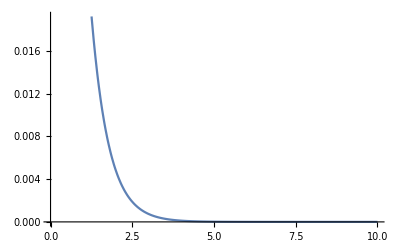

```mathematica
Plot[x[t],{t,0,10}]
```

```mathematica
(L2*Exp[L1*t]-L1*Exp[L2*t])/(Exp[L1*t]-Exp[L2*t])
```

```mathematica
Simplify[(0.1339745962155614 ⅇ^(-1.8660254037844386 t)-1.8660254037844386 ⅇ^(-0.1339745962155614 t))/(-ⅇ^(-1.8660254037844386 t)+ⅇ^(-0.1339745962155614 t))]
```

(0.133975 ⅇ^(-1.86603 t)-1.86603 ⅇ^(-0.133975 t))/(-ⅇ^(-1.86603 t)+ⅇ^(-0.133975 t))

```mathematica
L2-L1
```

-1.73205

```mathematica
(1/(L2-L1))*Log[A/B]
```

0.863755

```mathematica
A/B
```

0.

```mathematica
A
```

0.

```mathematica
(X*(((L2-L1)/2)-1))
```

-0.373205

```mathematica
(L2*X)
```

-0.373205

```mathematica
B
```

-0.34641

```mathematica
(X*(((L2-L1)/2)-1))
```

-0.373205

```mathematica
L2*X
```

-0.373205

```mathematica
L2*X
```

-0.373205

```mathematica
L2*y
```

-1.86603 y

```mathematica
L2*x
```

-1.86603 x

```mathematica
L2*X
```

-0.373205

```mathematica
L2
```

-1.86603

```mathematica
L1
```

-0.133975

```mathematica
X0-(X*L2)
```

-0.0001

```mathematica
X0-(X*L1)
```

-0.34651

```mathematica
(1/(L2-L1))*Log[A/B]
```

4.70569

```mathematica
A\B
```

```mathematica
A/B
```

0.000288592

```mathematica
A
```

-0.0001

```mathematica
B
```

-0.34651

```mathematica
A/B
```

0.000288592

```mathematica
Abs[a1-a2*a3]≤Abs[a1-a2*a4]
```

```mathematica
Simplify[Abs[a1-a2 a3]≤Abs[a1-a2 a4]]
```

Abs[a1-a2 a3]≤Abs[a1-a2 a4]

```mathematica
Abs[a1-a2*a3]
```

Abs[a1-a2 a3]

```mathematica
L2
```

-1.86603

```mathematica
L1
```

-0.133975

```mathematica
L2*X
```

-0.373205

```mathematica
x[t]
```

0.57735 (0.0267949 ⅇ^(-1.86603 t)-0.0267949 ⅇ^(-0.133975 t))+0.57735 (-0.0267949 ⅇ^(-1.86603 t)+0.373205 ⅇ^(-0.133975 t))

```mathematica
X0
```

-0.0267949